## Singular Perturbation

```mathematica
eq:={0.01 y''[t]+3y'[t]-(y[t])^4==0,y[0]==1,y[1]==1}
```

```mathematica
NDSolve[eq,y[t],{t,0,1}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
{yans[t_]}={y[t]}/.Flatten[NDSolve[eq,y[t],{t,0,1}]]
```

{InterpolatingFunction[…][t]}

```mathematica
graphy=Plot[yans[t],{t,0,1},AxesLabel->{"x","y"},PlotLabel->"Numerical Solution of y"];
```

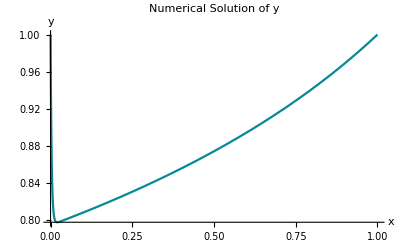

```mathematica
Show[graphy]
```

```mathematica
yhand[x_]:=1/(2-x)^(1/3)+(1-1/2^(1/3)  ) ⅇ^((-3x)/0.01)
```

```mathematica
graphyh=Plot[yhand[x],{x,0,1},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y",PlotStyle->Orange];
```

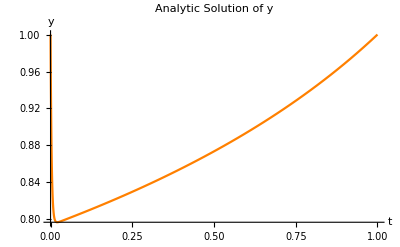

```mathematica
Show[graphyh]
```

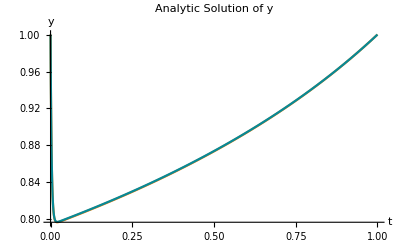

```mathematica
Show[graphyh,graphy]
```

```mathematica
eq2:={ϵ y''[t]+3y'[t]-(y[t])^4==0,y[0]==1,y[1]==1}
```

```mathematica
q=eq2/.y[t]->y0[t]+y1[t] ϵ+y2[t] ϵ^2+O[ϵ]^3//Simplify
```

{(-y0[t]^4+3 y'[t])+(-4 y0[t]^3 y1[t]+y''[t]) ϵ-2 (y0[t]^2 (3 y1[t]^2+2 y0[t] y2[t])) ϵ^2+O[ϵ]^3==0,y[0]==1,y[1]==1}

```mathematica
w=CoefficientList[q,ϵ]
```

{{(-y0[t]^4+3 y'[t])+(-4 y0[t]^3 y1[t]+y''[t]) ϵ-2 (y0[t]^2 (3 y1[t]^2+2 y0[t] y2[t])) ϵ^2+O[ϵ]^3==0},{y[0]==1},{y[1]==1}}

We attempt to solve for higher-order perturbations.

```mathematica
eqn=ϵy''[t]+3y'[t]-(y[t])^4;
```

```mathematica
p=eqn/.y->Function[{t},y0[t]+ϵ y1[t] + ϵ^2 y2[t] + O[ϵ]^3]
```

(-y0[t]^4+3 y0'[t]+ϵy''[t])+(-4 y0[t]^3 y1[t]+3 y1'[t]) ϵ+(-y0[t]^4 ((6 y1[t]^2)/y0[t]^2+(4 y2[t])/y0[t])+3 y2'[t]) ϵ^2+O[ϵ]^3

```mathematica
plist=CoefficientList[p,ϵ]
```

```mathematica
{-y0[t]^4+3 y0'[t]+ϵy''[t],-4 y0[t]^3 y1[t]+3 y1'[t],-y0[t]^4 ((6 y1[t]^2)/y0[t]^2+(4 y2[t])/y0[t])+3 y2'[t]}
```

```mathematica
DSolve[{-y0[t]^4+3 y0'[t]+ϵy''[t] == 0, y0[0] == 0}, y0, t]
```